Gezielte Suche für N=2000:

Gefundenes Minimum bei f = 68

Berechnetes A2: 0.12138064

Theoretisches A2: 0.12158542

Fehler: -0.1684 %

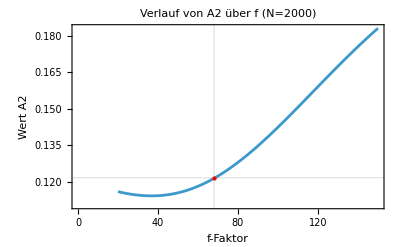

```mathematica
ClearAll["Global`*"];

(*1. Daten laden*)
path="C:/Users/sulta/git/cone-operator-lab/data/eigenvalues/box_eigs_exact_20000.txt";
allEigs=Sort@Select[Flatten@Import[path,"Table"]//N,#>0&];
nTest=2000;
eigsSub=allEigs[[1;;nTest]];
λN=Last[eigsSub];

(*2. Gezielter Minimum-Scan*)
factors=Range[20,150,1]; (*Feinere Auflösung*)
scanA2=Table[tMin=f/λN;tMax=500/λN;
tGrid=Exp@Subdivide[Log[tMin],Log[tMax],150];
Z=Total[Exp[-Outer[Times,eigsSub,tGrid]],{1}];
X=Table[t^{-3/2,-1,-1/2,0},{t,tGrid}];
coef=PseudoInverse[X].Z;
(coef[[3]]*(4 Pi)^(3/2))/(4 Pi^3),{f,factors}];

(*Theorie-Referenz nur zum Finden des Minimums im Plot*)
A2true=(1.0+1.5+2.3)/(4 Pi^2);
errors=Abs[scanA2/A2true-1];

(*Finde das f,bei dem der Fehler minimal ist*)
bestIdx=Ordering[errors,1][[1]];
fBest=factors[[bestIdx]];

(*3. Ergebnis-Ausgabe*)
A2hatBest=scanA2[[bestIdx]];

Print["Gezielte Suche für N=2000:"];
Print["Gefundenes Minimum bei f = ",fBest];
Print["Berechnetes A2: ",NumberForm[A2hatBest,8]];
Print["Theoretisches A2: ",NumberForm[A2true,8]];
Print["Fehler: ",NumberForm[100 (A2hatBest/A2true-1),4]," %"];

(*Kleiner Kontroll-Plot*)
ListLinePlot[Transpose[{factors,scanA2}],PlotLabel->"Verlauf von A2 über f (N=2000)",Frame->True,FrameLabel->{"f-Faktor","Wert A2"},Epilog->{Red,PointSize[Large],Point[{fBest,A2hatBest}]},GridLines->{{fBest},{A2true}}]
```